```mathematica
(*Equations A.6 and A.7  n=2 going towards 3 .... as rho -> 0 the dominant solution seems to be n=3 *)
Clear[mh,dmh,mw,i]
mh:=1;
dmh:=-0.40(*-0.23, -0.6,-0.281*);    (*0.70*) (*0.45*)
(*this bc only seem good up to -0.40*)
mw:=mh/2;
r0:=8.0; 
ar0:=0.28*√2(*0.28*);
dadrr0:=-0.248*√2; 
br0:=1.77;
dbdrr0:=-0.913;
rtarget:=(*0.006*)0.05;
artarget:=(*0.02349* 0.189*)0.19(*for test i used0.66*);
brtarget:=(*0.0002* 0.02*)0.007(*for test i used4*);
```

```mathematica
sol = NDSolve[{a''[r] -(mh^2+dmh)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[r0]==ar0,a[rtarget]==artarget,b[r0]==br0,b[rtarget]==brtarget},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[r0]==ar0,b[r0]==br0,a'[r0]==dadrr0,b'[r0]==dbdrr0}},MaxSteps->50000];

Abs[Evaluate[a[rtarget]/.sol]-artarget]
Abs[Evaluate[b[rtarget]/.sol]-brtarget]
Evaluate[a[rtarget]/.sol]
Evaluate[b[rtarget]/.sol]
```

NDSolve::ndsz: At r == 1.5584, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

{5.04898×10^-6}

{0.0000297035}

{0.190005}

{0.0069703}

```mathematica
Evaluate[a[rtarget]/.sol]
```

{0.270005}

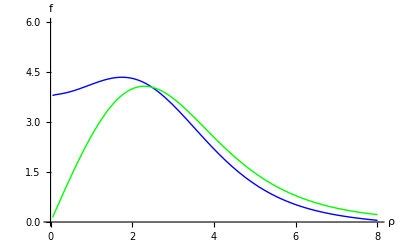

```mathematica
Plot[{(a[r]/.sol)/r,(b[r]/.sol)/r}, {r,0.05,8},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0},PlotRange->{0,6}]
(*a/r is blue   b/r is green*)
```

```mathematica
Options[WriteMatrix]={ColumnSeparator->"\t",FormatType->Identity};WriteMatrix[filename_String,data_List,opts___]:=Block[{myfile,op,colsep,ff},myfile=OpenWrite[filename];
colsep=ColumnSeparator/.{opts}/.Options[WriteMatrix];
ff=FormatType/.{opts}/.Options[WriteMatrix];
Scan[(WriteString[myfile,ff[First[#1]]];
Scan[WriteString[myfile,colsep,ff[#1]]&,Rest[#1]];
WriteString[myfile,"\n"])&,data];
Close[myfile]]
```

```mathematica
datapoints=TableForm[Table[{i,(a[i] /. sol[[1]])/i,(b[i] /. sol[[1]])/i},{i,0.05,8,0.5}]];
```

```mathematica
Write["integers.txt",OutputForm[TableForm[datapoints,TableSpacing->{0,3,3}]]];
Close["integers.txt"];
```